# CRNSSA Demo

```mathematica
<<CRNSSA`;
?CRNSSA`*
```

## Reaction System 0: f(x) = 1

```mathematica
rxnsys0 = {
rxnl[{x},{y},1],
rxnl[{y,y},{y},1],
init[{x, y},5]
};
GetSpecies[rxnsys0]
```

{x,y}

{{{5,5},{5,4},{5,3},{4,4},{4,3},{3,4},{3,3},{3,2},{3,1},{2,2},{2,1},{1,2},{0,3},{0,2},{0,1}},{0.,0.0245508,0.151592,0.186375,0.21456,0.221926,0.278016,0.437066,0.533669,1.2354,1.39671,1.46192,1.48511,1.53898,1.64882}}

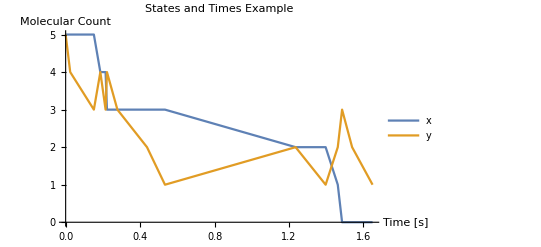

```mathematica
SimulateDirectSSA[rxnsys0,outputTS->False]
PlotLastSimulation[PlotLabel->"States and Times Example"]
```

{{5,5},{5,4},{5,3},{5,2},{5,1},{4,2},{3,3},{3,2},{3,1},{2,2},{1,3},{1,2},{1,1},{0,2},{0,1}}

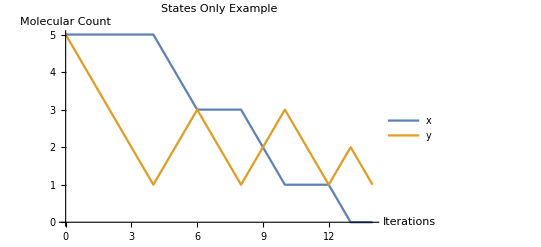

```mathematica
SimulateDirectSSA[rxnsys0,statesOnly->True,outputTS->False]
PlotLastSimulation[PlotLabel->"States Only Example"]
```

## Reaction System 1: Demonstrating functionality and automatic processing of objects

```mathematica
rxnsys1={
rxn[0,2x+3y+8z[j-k][j+k],3],
revrxn[z[j+k][j-k],1,4,5],
rxnl[{},{z[j+k][j-k],z[j-k][j+k],x,x},10],
init[a, 10],
init[{a,b,x,y},1000]
};
GetSpecies[rxnsys1]
```

{a,b,x,y,z[j-k][j+k],z[j+k][j-k]}

```mathematica
GetSpecies[rxnsys1, z[_][_]]
```

{z[j-k][j+k],z[j+k][j-k]}

```mathematica
SimulateDirectSSA[rxnsys1,iterEnd->15,useIter->True,statesOnly->True,outputTS->False]
```

{{1010,1000,1000,1000,0,0},{1010,1000,1002,1000,1,1},{1010,1000,1004,1003,9,1},{1010,1000,1004,1003,9,2},{1010,1000,1004,1003,9,1},{1010,1000,1006,1003,10,2},{1010,1000,1008,1003,11,3},{1010,1000,1008,1003,11,2},{1010,1000,1010,1003,12,3},{1010,1000,1010,1003,12,4},{1010,1000,1010,1003,12,3},{1010,1000,1010,1003,12,4},{1010,1000,1012,1003,13,5},{1010,1000,1012,1003,13,4},{1010,1000,1014,1003,14,5},{1010,1000,1014,1003,14,6}}

```mathematica
SimulateDirectSSA[rxnsys1,iterEnd->15,useIter->True,finalOnly->True,outputTS->False]
```

{{{1010,1000,1010,1006,19,3}},{0.671941}}

## Reaction System 2: A deterministic CRN

```mathematica
rxnsys2={
rxn[x1,y+z1,2],
rxn[x2,y+z2,2],
rxn[z1+z2,k,1],
rxn[k+y,1,3],
init[x1,5],
init[x2,15]
};
GetSpecies[rxnsys2]
```

{k,x1,x2,y,z1,z2}

TimeSeries[…]

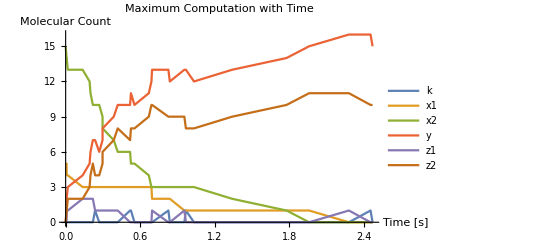

```mathematica
SimulateDirectSSA[rxnsys2]
PlotLastSimulation[PlotLabel->"Maximum Computation with Time"]
```

TimeSeries[…]

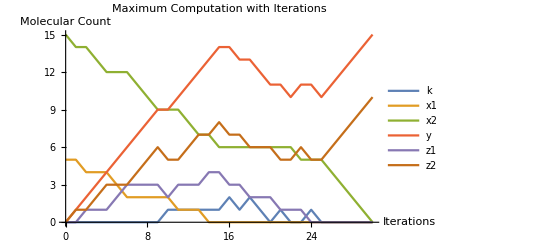

```mathematica
SimulateDirectSSA[rxnsys2,statesOnly->True]
PlotLastSimulation[PlotLabel->"Maximum Computation with Iterations"]
```

```mathematica
SimulateDirectSSA[rxnsys2,statesOnly->True,finalOnly->True,outputTS->False]
GetSpecies[rxnsys2]
```

{{0,0,0,15,0,10}}

{k,x1,x2,y,z1,z2}

## Reaction System 3: Demonstrating erroneous input handling

```mathematica
rxnsys3={
rxn[a,b,1],
rxn[c,d,2,3],
rxxn[e,f,4],
reaction[g,h,5],
revrxn[i,j,6,7],
revrxn[k,l,8],
rxnl[{m},{},9],
rxnl[o,p,10],
init[10],
init[{a,b,c,d, e, f, g, h},20],
inits[{i, j, k, l, m, o , p},30]
};
GetSpecies[rxnsys3]
```

GetSpecies::rxnsyswarn: Warning: Unknown objects detected in rxnsys. These will be ignored by Wolfram pattern matching: {rxn[c,d,2,3],rxxn[e,f,4],reaction[g,h,5],revrxn[k,l,8],rxnl[o,p,10],init[10],inits[{i,j,k,l,m,o,p},30]}

{a,b,c,d,e,f,g,h,i,j,m}

```mathematica
SimulateDirectSSA[rxnsys3,iterEnd->0.5,useIter->True,finalOnly->True]
PlotLastSimulation[]
```

SimulateDirectSSA::rxnsyswarn: Warning: Unknown objects detected in rxnsys. These will be ignored by Wolfram pattern matching: {rxn[c,d,2,3],rxxn[e,f,4],reaction[g,h,5],revrxn[k,l,8],rxnl[o,p,10],init[10],inits[{i,j,k,l,m,o,p},30]}

SimulateDirectSSA::iterenderr: Error: iterEnd (0.5) must be an integer greater than zero

TimeSeries[…]

PlotLastSimulation::finalonlyerr: Error: Cannot plot when finalOnly = True